# Laboratorio 3, Mat1620L

## Preguntas

### 1)

#### Solución

a) Ocuparemos una forma alternativa ocupando las funcionalidades del software. Graficaremos el error y veremos donde debería estar el optimo buscado.

```mathematica
f[x_]:=Cos[x]
p8[x_]:=Normal[Series[f[t],{t,0,8}]]/.t->x
p10[x_]:=Normal[Series[f[t],{t,0,10}]]/.t->x
```

Graficamos el error

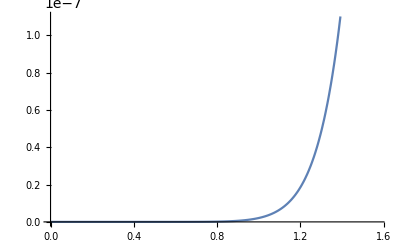

```mathematica
Error[x_]:=Abs[p10[x]-Cos[x]]
Plot[Error[x],{x,0,Pi/2}]
```

Vemos que el error es máximo en x=π/2. El siguiente código muestra que el error es menor que 5×10^-7.

```mathematica
Error[Pi/2]<5*10^(-7)
```

True

Si vemos el gráfico de p_10(x) junto con Cos(x) en [0,π/2] notaremos que la aproximación es bastante buena.

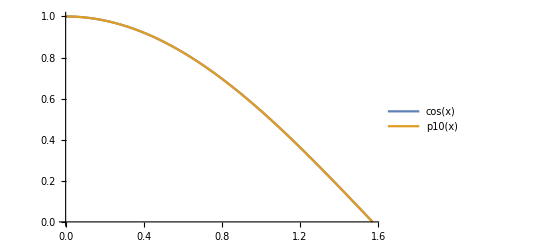

```mathematica
Plot[{Cos[x],p10[x]},{x,0,Pi/2},PlotLegends->"Expressions"]
```

b)

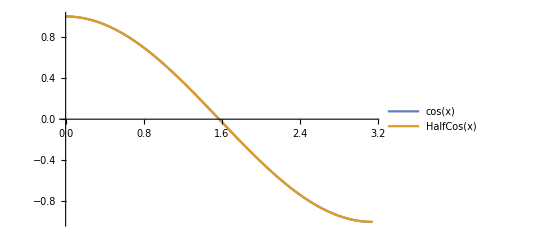

```mathematica
(*Tambien se puede ocupar Piecewise en vez de halfcos[x_]:=If[0≤ x≤Pi/2,p10[x],-p10[Pi-x]]*)
HalfCos[x_]:=Piecewise[{{p10[x],0≤ x≤Pi/2},{-p10[Pi-x],Pi/2<x≤ Pi}}];
Plot[{Cos[x],HalfCos[x]},{x,0,Pi},PlotLegends->"Expressions"]
```

c)

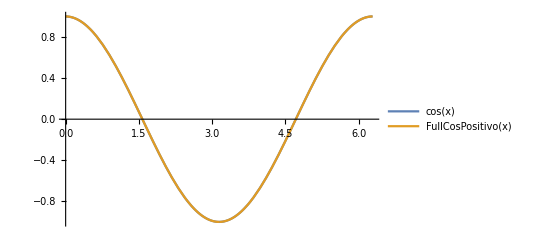

```mathematica
(*Tambien se puede ocupar Piecewise en vez de fullcos[x_]:=If[x≤Pi,halfcos[x],halfcos[2*Pi-x]]*)

FullCosPositivo[x_]:=Piecewise[{{halfcos[x],0≤ x≤Pi},{halfcos[2*Pi-x],Pi<x≤2 Pi}}];
Plot[{Cos[x],FullCosPositivo[x]},{x,0,2*Pi},PlotLegends->"Expressions"]
```

d) Todo lo anterior sumando que cos(x) es par. La función fullcos esta definida en [-2π,2π].

```mathematica
FullCos[x_]:=Piecewise[{{FullCosPositivo[x],x≥ 0},{FullCosPositivo[-x],x<0}}]
```

e)

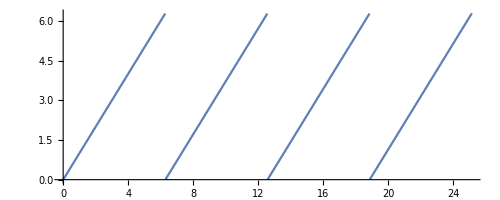

```mathematica
shift[x_]:=x-2*Pi*Floor[x/(2*Pi)]
Plot[shift[x],{x,0,8*Pi},AspectRatio->Automatic]
```

f) Ocupando shift[x] expandimos fullcos[x] a todo R.

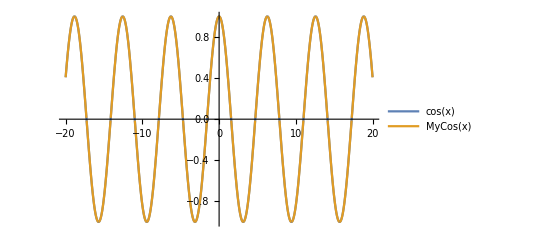

```mathematica
MyCos[x_]:=FullCos[shift[x]]
Plot[{Cos[x],MyCos[x]},{x,-20,20},PlotLegends->"Expressions"]
```